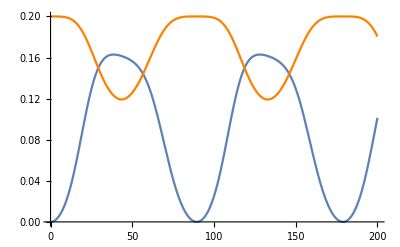

```mathematica
ClearAll["Global`*"];
subtractAngles[a1_,a2_]:=(
d=Abs[a1-a2];
Return[Min[d,2*Pi-d]];
);
angularError[vec_,vecError_,rx_,ry_,rz_,t_,i_]:=(
sphericalVec=ToSphericalCoordinates[vec.MatrixPower[N[EulerMatrix[{rx,ry,rz}]],t]];
sphericalVecError=ToSphericalCoordinates[vecError.MatrixPower[N[EulerMatrix[{rx,ry,rz}]],t]];
Return[subtractAngles[sphericalVec[[i]],sphericalVecError[[i]]]];
);
elevationError=Plot[angularError[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],Pi/100,Pi/100,Pi/100,t,2],{t,0,200},PlotStyle->Orange];
azimuthalError=Plot[angularError[{1,0,0},N[{1,0,0}.EulerMatrix[{0,0.2,0}]],Pi/100,Pi/100,Pi/100,t,3],{t,0,200}];
Show[azimuthalError,elevationError,PlotRange->All]
```